```mathematica
SetDirectory["C:/MessdatenEingang"];
Dateien=FileNames[];
Framed[ListPicker[Dynamic[px],Dateien],FrameStyle->Green,RoundingRadius->10]
```

$CellContext`px

```mathematica
filename=px;
OrdnerInhalt=FileNames["*",filename];
SetDirectory["C:/MessdatenEingang/"<>filename];
textDateien =FileNames["*.txt"] ;
gelDatei=Import[textDateien[[1]], "Data"] ; (* Importiere die .txtDatei  *)
Manipulate[gelDatei[[i]],{i,0,22,1}] (* Manipulate über die Zeilenm*)
(* Nehme die Zeilen mit Informationen über die Probe *)
FilterKombo= gelDatei[[11]][[2]];
IntegZeit= Quantity[gelDatei[[8]][[2]],"s"];
ProbenName = ToString[gelDatei[[4]][[2]]];
Temp = Quantity[gelDatei[[7]][[2]],"Kelvin"];
ExcPow= Quantity[gelDatei[[20]][[2]],"kilowatt per cm^2"];
```

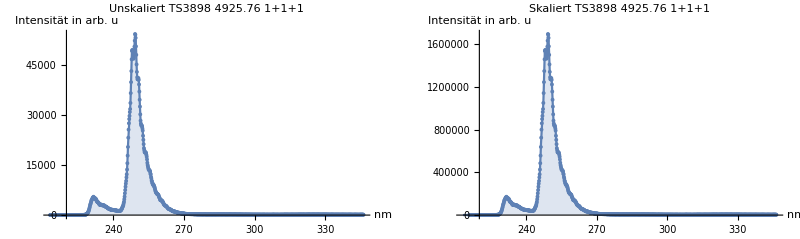
{{Null^8 -Graphics-,□}}

```mathematica
{{f = Interpolation[gelDatei[[21;; All]],InterpolationOrder->1];
skalFaktor= QuantityMagnitude[1/IntegZeit];
gelDateiSkal= gelDatei[[21 ;;All]];
gelDateiSkal[[All,2]]=gelDateiSkal[[All,2]] * skalFaktor;
(*Integrate[f,{x,f[[1]][[1]][[1]],f[[1]][[1]][[2]]}]*)
integInt=Integrate[f[x],{x,f[[1]][[1]][[1]],f[[1]][[1]][[2]]}]*skalFaktor;
PlotTitel= ProbenName<> " " <>ToString[QuantityMagnitude[ExcPow]] <> " " <> ToString[FilterKombo];

p1 = Show[Plot[f[x],{x,f[[1]][[1]][[1]],f[[1]][[1]][[2]]} , Filling->Axis,PlotRange->Full, Axes-> True,AxesLabel->{" nm","Intensität in arb. u"},PlotLabel->"Unskaliert"<> " " <> PlotTitel],ListPlot[gelDatei[[21;; All]], Axes->True,PlotRange-> Automatic]];
p2= Show[Plot[f[x]*skalFaktor,{x,f[[1]][[1]][[1]],f[[1]][[1]][[2]]} , Filling->Axis,PlotRange->Full, Axes-> True,AxesLabel->{" nm","Intensität in arb. u"},PlotLabel->"Skaliert"<> " " <> PlotTitel],ListPlot[gelDateiSkal[[21;; All]], Axes->True,PlotRange-> Automatic]];
GraphicsGrid[{{p1,p2}},ImageSize-> 800], □}}
```

```mathematica
dataset=Dataset[{
<|"FilterKombo"->FilterKombo,"Temp"->QuantityMagnitude[Temp],"Integrationszeit"->IntegZeit,"ProbenName"->ProbenName,"Anregungsleistungsdichte"-> ExcPow,"Datenpunkte"-> gelDateiSkal[[1 ;;All]]|>}]
```

```mathematica
filename=px;
OrdnerInhalt=FileNames["*",filename];
SetDirectory["C:/MessdatenEingang/"<>filename];
textDateien =FileNames["*.txt"] ;
gelDatei=Import[textDateien[[1]], "Data"] ; (* Importiere die .txtDatei  *)
Manipulate[gelDatei[[i]],{i,0,22,1}] (* Manipulate über die Zeilenm*)
(* Nehme die Zeilen mit Informationen über die Probe *)
FilterKombo= gelDatei[[11]][[2]];
IntegZeit= Quantity[gelDatei[[8]][[2]],"s"];
ProbenName = ToString[gelDatei[[4]][[2]]];
Temp = Quantity[gelDatei[[7]][[2]],"Kelvin"];
ExcPow= Quantity[gelDatei[[20]][[2]],"kilowatt per cm^2"];
datasetTest=Dataset[{
<|"FilterKombo"->FilterKombo,"Temp"->QuantityMagnitude[Temp],"Integrationszeit"->QuantityMagnitude[IntegZeit],"ProbenName"->ProbenName,"Anregungsleistungsdichte"-> QuantityMagnitude[ExcPow],"Integrierte Int."->QuantityMagnitude[integInt]|>}]
```

```mathematica
Table[
gelDatei=Import[textDateien[[i]], "Data"];
FilterKombo= gelDatei[[11]][[2]];
IntegZeit= Quantity[gelDatei[[8]][[2]],"s"];
ProbenName = ToString[gelDatei[[4]][[2]]];
Temp = Quantity[gelDatei[[7]][[2]],"Kelvin"];
ExcPow= Quantity[gelDatei[[20]][[2]],"kilowatt per cm^2"];
skalFaktor= QuantityMagnitude[1/IntegZeit];
f = Interpolation[gelDatei[[21;; All]],InterpolationOrder->1];
skalFaktor= QuantityMagnitude[1/IntegZeit];
gelDateiSkal= gelDatei[[21 ;;All]];
gelDateiSkal[[All,2]] * skalFaktor;
integInt=Integrate[f[x],{x,f[[1]][[1]][[1]],f[[1]][[1]][[2]]}]*skalFaktor;
datasetTest =AppendTo[datasetTest,<|"FilterKombo"->FilterKombo,"Temp"->QuantityMagnitude[Temp],"Integrationszeit"->QuantityMagnitude[IntegZeit],"ProbenName"->ProbenName,"Anregungsleistungsdichte"-> QuantityMagnitude[ExcPow],"Integrierte Int."->QuantityMagnitude[integInt]|>];,{i,2,100,1}]
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
datasetTest
```

```mathematica
Information[datasetTest]
```

Global`datasetTest

datasetTest=

```mathematica
gelDatei:=Import[textDateien[[3]], "Data"]
FilterKombo:= gelDatei[[11]][[2]]
IntegZeit:= Quantity[gelDatei[[8]][[2]],"s"]
ProbenName := ToString[gelDatei[[4]][[2]]]
Temp := Quantity[gelDatei[[7]][[2]],"Kelvin"]
ExcPow:= Quantity[gelDatei[[20]][[2]],"kilowatt per cm^2"]
skalFaktor:= QuantityMagnitude[1/IntegZeit]
f := Interpolation[gelDatei[[21;; All]],InterpolationOrder->1]
skalFaktor:= QuantityMagnitude[1/IntegZeit]
gelDateiSkal:= gelDatei[[21 ;;All]]
gelDateiSkal[[All,2]]* skalFaktor
integInt:=Integrate[f[x],{x,f[[1]][[1]][[1]],f[[1]][[1]][[2]]}]*skalFaktor;
datasetTest=AppendTo[datasetTest,<|"FilterKombo"->FilterKombo,"Temp"->QuantityMagnitude[Temp],"Integrationszeit"->QuantityMagnitude[IntegZeit],"ProbenName"->ProbenName,"Anregungsleistungsdichte"-> QuantityMagnitude[ExcPow],"Integrierte Int."->QuantityMagnitude[integInt],"Datenpunkte"->gelDateiSkal|>]
```

{476.19,190.476,380.952,285.714,666.667,333.333,333.333,380.952,142.857,857.143,333.333,476.19,285.714,476.19,47.619,1047.62,380.952,238.095,666.667,380.952,714.286,619.048,428.571,285.714,619.048,190.476,428.571,666.667,666.667,428.571,809.524,571.429,523.81,523.81,285.714,523.81,571.429,761.905,285.714,1000.,571.429,476.19,571.429,285.714,571.429,619.048,857.143,428.571,476.19,333.333,428.571,904.762,428.571,952.381,809.524,714.286,571.429,476.19,380.952,857.143,952.381,523.81,904.762,809.524,380.952,285.714,1142.86,476.19,523.81,761.905,476.19,428.571,1285.71,1047.62,904.762,952.381,666.667,476.19,571.429,571.429,619.048,809.524,1047.62,1095.24,1000.,714.286,571.429,1095.24,809.524,714.286,904.762,666.667,1142.86,1095.24,1000.,857.143,1095.24,1142.86,1142.86,952.381,904.762,1190.48,1238.1,904.762,1761.9,1238.1,1666.67,1380.95,1523.81,1476.19,1428.57,1809.52,1904.76,2380.95,2952.38,2904.76,3523.81,5047.62,5714.29,7476.19,9761.9,11857.1,15476.2,19190.5,25190.5,30476.2,37047.6,44285.7,54381.,62809.5,70523.8,82047.6,91238.1,98428.6,105286.,114524.,116905.,125238.,131476.,131571.,134000.,135714.,132048.,134095.,128524.,125714.,125048.,122571.,121000.,116381.,111571.,107714.,104190.,100048.,95000.,93761.9,92095.2,89904.8,86761.9,82809.5,80190.5,79047.6,77761.9,77000.,76047.6,76714.3,75095.2,75666.7,76238.1,73285.7,74142.9,73904.8,70142.9,73142.9,72142.9,70333.3,71714.3,69095.2,66333.3,64714.3,64714.3,63714.3,62285.7,60952.4,59761.9,57047.6,54761.9,53476.2,49857.1,50285.7,47904.8,47809.5,46761.9,46000.,43809.5,43523.8,42761.9,42428.6,41381.,40809.5,38619.,41000.,39428.6,39381.,38857.1,38238.1,38761.9,38095.2,38047.6,36523.8,36619.,36904.8,36000.,35571.4,34523.8,33761.9,32095.2,31857.1,31619.,31952.4,31095.2,30714.3,30381.,31333.3,30142.9,30904.8,30476.2,31095.2,32285.7,33952.4,35666.7,39142.9,40904.8,47285.7,51333.3,56619.,61428.6,68666.7,76142.9,87428.6,97619.,114667.,133286.,159810.,183857.,210905.,231238.,255429.,277000.,302095.,335952.,388190.,438333.,504333.,566810.,628667.,677524.,716000.,744286.,758381.,789857.,836333.,901667.,994048.,1.08471×10^6,1.16229×10^6,1.21667×10^6,1.24081×10^6,1.22886×10^6,1.20276×10^6,1.1731×10^6,1.1659×10^6,1.17248×10^6,1.207×10^6,1.2581×10^6,1.30014×10^6,1.34557×10^6,1.34714×10^6,1.3251×10^6,1.2571×10^6,1.19614×10^6,1.12724×10^6,1.07362×10^6,1.02767×10^6,1.02095×10^6,1.01995×10^6,1.02457×10^6,1.01605×10^6,1.00095×10^6,973286.,921333.,856619.,800333.,736524.,707524.,679429.,670429.,666857.,658381.,650810.,639952.,622667.,584000.,561619.,521476.,504238.,485143.,469905.,466286.,464571.,465286.,459857.,457048.,451190.,433905.,413857.,396619.,376381.,360952.,352571.,345000.,341286.,339952.,333190.,326810.,322000.,305000.,297571.,282714.,268810.,258857.,246286.,238810.,233048.,227714.,227143.,221095.,219857.,213429.,206762.,196143.,192095.,179952.,174429.,166905.,164667.,159667.,157000.,154381.,152333.,154238.,151952.,146381.,137476.,137286.,129762.,124524.,119524.,115476.,111286.,110429.,108000.,107238.,104762.,102333.,99190.5,96476.2,94428.6,87381.,81761.9,75857.1,74809.5,73571.4,71904.8,69523.8,69238.1,66285.7,66428.6,64000.,61047.6,59047.6,56333.3,53000.,49666.7,48523.8,45571.4,45523.8,44285.7,43619.,42428.6,41428.6,40619.,38619.,38428.6,35952.4,34809.5,33142.9,31714.3,30285.7,27857.1,28142.9,28095.2,26857.1,26904.8,27476.2,26190.5,24571.4,24000.,22904.8,22095.2,20904.8,19857.1,18714.3,19142.9,17857.1,17428.6,17904.8,16523.8,17666.7,16714.3,16238.1,15571.4,15000.,14619.,14047.6,13761.9,13000.,12381.,11666.7,11428.6,11714.3,11095.2,11571.4,11952.4,10761.9,10857.1,10428.6,9285.71,9476.19,8904.76,9285.71,9190.48,8619.05,8523.81,8476.19,8809.52,8619.05,7857.14,8333.33,7857.14,7952.38,7761.9,7333.33,7523.81,7000.,7142.86,7095.24,6714.29,6809.52,6047.62,6428.57,5952.38,6476.19,6761.9,5952.38,6238.1,6476.19,6523.81,5476.19,5952.38,5761.9,5285.71,5380.95,5095.24,5285.71,5380.95,5095.24,4952.38,5285.71,5285.71,5523.81,5047.62,5095.24,4666.67,5333.33,5190.48,5142.86,5047.62,4523.81,4857.14,4761.9,4714.29,4523.81,4952.38,4619.05,4428.57,4952.38,4619.05,4190.48,4571.43,5047.62,4428.57,4095.24,3857.14,4809.52,4333.33,4285.71,3809.52,3857.14,4714.29,4380.95,4619.05,4428.57,4523.81,4333.33,4238.1,4761.9,4571.43,4809.52,4047.62,4666.67,4333.33,3952.38,4523.81,4285.71,4380.95,4000.,4000.,4190.48,4809.52,3904.76,4571.43,4714.29,4238.1,4333.33,4619.05,4238.1,4571.43,4904.76,4809.52,4047.62,4523.81,4523.81,4714.29,4285.71,4142.86,4428.57,4428.57,4809.52,4333.33,4809.52,4809.52,5095.24,4809.52,4238.1,4190.48,4380.95,4142.86,4047.62,4285.71,4380.95,4285.71,4571.43,4428.57,4571.43,4285.71,4857.14,4095.24,5000.,4142.86,4571.43,4523.81,4619.05,4428.57,4238.1,3952.38,4380.95,4523.81,5190.48,4047.62,4476.19,4238.1,4428.57,4619.05,4333.33,4714.29,4571.43,4333.33,4571.43,4285.71,4285.71,4333.33,4238.1,3952.38,3619.05,4285.71,4142.86,3952.38,4047.62,3571.43,4238.1,4142.86,4476.19,4476.19,4095.24,4380.95,4523.81,4666.67,4238.1,3857.14,3238.1,3857.14,3333.33,4142.86,4142.86,3571.43,4523.81,3238.1,4095.24,3619.05,3761.9,3666.67,4238.1,3476.19,3523.81,3238.1,3666.67,3666.67,3523.81,4095.24,3047.62,3095.24,3523.81,3523.81,3857.14,3619.05,3857.14,3476.19,3285.71,3714.29,3761.9,3809.52,3523.81,3523.81,3904.76,3380.95,3380.95,3428.57,3238.1,3333.33,3285.71,3190.48,3238.1,3095.24,3142.86,3428.57,3142.86,3523.81,2761.9,2857.14,3523.81,2523.81,2809.52,3476.19,3714.29,3428.57,2857.14,2952.38,3380.95,3380.95,3285.71,3142.86,2714.29,3523.81,3333.33,2428.57,3047.62,2809.52,2904.76,3142.86,3380.95,3238.1,2714.29,3428.57,3000.,3238.1,3380.95,3238.1,2904.76,2857.14,2809.52,2857.14,3238.1,2904.76,2952.38,2666.67,3047.62,2714.29,2952.38,2809.52,3047.62,2952.38,2714.29,2904.76,2857.14,3095.24,3380.95,3285.71,2571.43,2619.05,2857.14,2619.05,2809.52,2809.52,3000.,2857.14,2571.43,2428.57,3285.71,3095.24,2904.76,3095.24,2809.52,2619.05,3238.1,2952.38,3333.33,2857.14,2809.52,2761.9,3095.24,2904.76,3285.71,3095.24,2666.67,3047.62,2809.52,2857.14,2952.38,2904.76,3142.86,2666.67,2761.9,2857.14,3047.62,2523.81,2619.05,2904.76,3095.24,3000.,2952.38,2476.19,2857.14,3333.33,3142.86,3190.48,3238.1,2952.38,3095.24,2952.38,3047.62,2904.76,2952.38,3571.43,3285.71,3238.1,2904.76,2761.9,3238.1,2809.52,3476.19,3333.33,2809.52,3571.43,3238.1,3095.24,3285.71,2666.67,3285.71,3428.57,3142.86,3190.48,3000.,2761.9,3380.95,3380.95,3523.81,3047.62,3190.48,3571.43,3380.95,3476.19,3714.29,2857.14,3190.48,3761.9,3142.86,3571.43,3428.57,3142.86,3714.29,3285.71,3619.05,3523.81,3333.33,3095.24,3285.71,3333.33,3761.9,3619.05,2952.38,3333.33,3809.52,3619.05,3380.95,3238.1,3428.57,3571.43,4095.24,3428.57,3380.95,3380.95,2904.76,3761.9,3666.67,3380.95,3333.33,3428.57,3619.05,3523.81,3047.62,3142.86,2523.81,3333.33,3857.14,3904.76,3809.52,3809.52,3809.52,3476.19,3619.05,3952.38,3714.29,3761.9,3333.33,3857.14,3904.76,3666.67,3619.05,3809.52,3523.81,4285.71,3904.76,3904.76,3523.81,3619.05,3619.05,3285.71,3142.86,4095.24,3571.43,3761.9,3619.05,3666.67,3571.43,3714.29,3857.14,3761.9,3571.43,3952.38,3380.95,3761.9,3904.76,3571.43,3619.05,3761.9,3809.52,3285.71,3857.14,3571.43,3428.57,3142.86,3714.29,3952.38,3428.57,3761.9,3523.81,3333.33,3047.62,2904.76,3333.33,3619.05,3238.1,3619.05,3809.52,3523.81,3333.33,3142.86,3333.33,3714.29,3619.05,2952.38,2952.38,3285.71,3238.1,3190.48,3333.33,3761.9,3476.19,3380.95,3333.33,3380.95,3666.67,3380.95,3333.33,3333.33,3142.86,3285.71,3095.24,3000.,2714.29,3714.29,3190.48,3333.33,3333.33,4047.62,3523.81,3190.48,3095.24,3809.52,3190.48,3285.71,2809.52,2857.14,2857.14,2428.57,3047.62,3761.9,3095.24,3095.24,3285.71,2857.14,3285.71,3000.,3190.48,3333.33,3000.,3095.24,3238.1,2809.52,3000.,2952.38,3523.81,3285.71,2857.14,3380.95,2809.52,3476.19,2714.29,3047.62,3571.43,3047.62,2809.52,2714.29,3095.24,3000.,3095.24,3142.86,3190.48,3000.,2666.67,2857.14,2857.14,3142.86,2761.9,2952.38,3190.48,2523.81,2857.14,2761.9,2904.76,2619.05,3190.48,2809.52,3095.24,2666.67,2714.29,2761.9,2714.29,3428.57,2809.52,3000.,2809.52,2809.52,2857.14,3190.48,3428.57,3047.62,3000.,2666.67,2904.76,3095.24,3047.62,2904.76,2952.38,2571.43,2619.05,2285.71,2523.81,2761.9,3190.48,2761.9,3380.95,2809.52,2809.52,2428.57,3142.86,3428.57,3142.86,2761.9,2523.81,2714.29,3000.,2523.81}

Set::noval: Symbol gelDateiSkal in part assignment does not have an immediate value.

{476.19,190.476,380.952,285.714,666.667,333.333,333.333,380.952,142.857,857.143,333.333,476.19,285.714,476.19,47.619,1047.62,380.952,238.095,666.667,380.952,714.286,619.048,428.571,285.714,619.048,190.476,428.571,666.667,666.667,428.571,809.524,571.429,523.81,523.81,285.714,523.81,571.429,761.905,285.714,1000.,571.429,476.19,571.429,285.714,571.429,619.048,857.143,428.571,476.19,333.333,428.571,904.762,428.571,952.381,809.524,714.286,571.429,476.19,380.952,857.143,952.381,523.81,904.762,809.524,380.952,285.714,1142.86,476.19,523.81,761.905,476.19,428.571,1285.71,1047.62,904.762,952.381,666.667,476.19,571.429,571.429,619.048,809.524,1047.62,1095.24,1000.,714.286,571.429,1095.24,809.524,714.286,904.762,666.667,1142.86,1095.24,1000.,857.143,1095.24,1142.86,1142.86,952.381,904.762,1190.48,1238.1,904.762,1761.9,1238.1,1666.67,1380.95,1523.81,1476.19,1428.57,1809.52,1904.76,2380.95,2952.38,2904.76,3523.81,5047.62,5714.29,7476.19,9761.9,11857.1,15476.2,19190.5,25190.5,30476.2,37047.6,44285.7,54381.,62809.5,70523.8,82047.6,91238.1,98428.6,105286.,114524.,116905.,125238.,131476.,131571.,134000.,135714.,132048.,134095.,128524.,125714.,125048.,122571.,121000.,116381.,111571.,107714.,104190.,100048.,95000.,93761.9,92095.2,89904.8,86761.9,82809.5,80190.5,79047.6,77761.9,77000.,76047.6,76714.3,75095.2,75666.7,76238.1,73285.7,74142.9,73904.8,70142.9,73142.9,72142.9,70333.3,71714.3,69095.2,66333.3,64714.3,64714.3,63714.3,62285.7,60952.4,59761.9,57047.6,54761.9,53476.2,49857.1,50285.7,47904.8,47809.5,46761.9,46000.,43809.5,43523.8,42761.9,42428.6,41381.,40809.5,38619.,41000.,39428.6,39381.,38857.1,38238.1,38761.9,38095.2,38047.6,36523.8,36619.,36904.8,36000.,35571.4,34523.8,33761.9,32095.2,31857.1,31619.,31952.4,31095.2,30714.3,30381.,31333.3,30142.9,30904.8,30476.2,31095.2,32285.7,33952.4,35666.7,39142.9,40904.8,47285.7,51333.3,56619.,61428.6,68666.7,76142.9,87428.6,97619.,114667.,133286.,159810.,183857.,210905.,231238.,255429.,277000.,302095.,335952.,388190.,438333.,504333.,566810.,628667.,677524.,716000.,744286.,758381.,789857.,836333.,901667.,994048.,1.08471×10^6,1.16229×10^6,1.21667×10^6,1.24081×10^6,1.22886×10^6,1.20276×10^6,1.1731×10^6,1.1659×10^6,1.17248×10^6,1.207×10^6,1.2581×10^6,1.30014×10^6,1.34557×10^6,1.34714×10^6,1.3251×10^6,1.2571×10^6,1.19614×10^6,1.12724×10^6,1.07362×10^6,1.02767×10^6,1.02095×10^6,1.01995×10^6,1.02457×10^6,1.01605×10^6,1.00095×10^6,973286.,921333.,856619.,800333.,736524.,707524.,679429.,670429.,666857.,658381.,650810.,639952.,622667.,584000.,561619.,521476.,504238.,485143.,469905.,466286.,464571.,465286.,459857.,457048.,451190.,433905.,413857.,396619.,376381.,360952.,352571.,345000.,341286.,339952.,333190.,326810.,322000.,305000.,297571.,282714.,268810.,258857.,246286.,238810.,233048.,227714.,227143.,221095.,219857.,213429.,206762.,196143.,192095.,179952.,174429.,166905.,164667.,159667.,157000.,154381.,152333.,154238.,151952.,146381.,137476.,137286.,129762.,124524.,119524.,115476.,111286.,110429.,108000.,107238.,104762.,102333.,99190.5,96476.2,94428.6,87381.,81761.9,75857.1,74809.5,73571.4,71904.8,69523.8,69238.1,66285.7,66428.6,64000.,61047.6,59047.6,56333.3,53000.,49666.7,48523.8,45571.4,45523.8,44285.7,43619.,42428.6,41428.6,40619.,38619.,38428.6,35952.4,34809.5,33142.9,31714.3,30285.7,27857.1,28142.9,28095.2,26857.1,26904.8,27476.2,26190.5,24571.4,24000.,22904.8,22095.2,20904.8,19857.1,18714.3,19142.9,17857.1,17428.6,17904.8,16523.8,17666.7,16714.3,16238.1,15571.4,15000.,14619.,14047.6,13761.9,13000.,12381.,11666.7,11428.6,11714.3,11095.2,11571.4,11952.4,10761.9,10857.1,10428.6,9285.71,9476.19,8904.76,9285.71,9190.48,8619.05,8523.81,8476.19,8809.52,8619.05,7857.14,8333.33,7857.14,7952.38,7761.9,7333.33,7523.81,7000.,7142.86,7095.24,6714.29,6809.52,6047.62,6428.57,5952.38,6476.19,6761.9,5952.38,6238.1,6476.19,6523.81,5476.19,5952.38,5761.9,5285.71,5380.95,5095.24,5285.71,5380.95,5095.24,4952.38,5285.71,5285.71,5523.81,5047.62,5095.24,4666.67,5333.33,5190.48,5142.86,5047.62,4523.81,4857.14,4761.9,4714.29,4523.81,4952.38,4619.05,4428.57,4952.38,4619.05,4190.48,4571.43,5047.62,4428.57,4095.24,3857.14,4809.52,4333.33,4285.71,3809.52,3857.14,4714.29,4380.95,4619.05,4428.57,4523.81,4333.33,4238.1,4761.9,4571.43,4809.52,4047.62,4666.67,4333.33,3952.38,4523.81,4285.71,4380.95,4000.,4000.,4190.48,4809.52,3904.76,4571.43,4714.29,4238.1,4333.33,4619.05,4238.1,4571.43,4904.76,4809.52,4047.62,4523.81,4523.81,4714.29,4285.71,4142.86,4428.57,4428.57,4809.52,4333.33,4809.52,4809.52,5095.24,4809.52,4238.1,4190.48,4380.95,4142.86,4047.62,4285.71,4380.95,4285.71,4571.43,4428.57,4571.43,4285.71,4857.14,4095.24,5000.,4142.86,4571.43,4523.81,4619.05,4428.57,4238.1,3952.38,4380.95,4523.81,5190.48,4047.62,4476.19,4238.1,4428.57,4619.05,4333.33,4714.29,4571.43,4333.33,4571.43,4285.71,4285.71,4333.33,4238.1,3952.38,3619.05,4285.71,4142.86,3952.38,4047.62,3571.43,4238.1,4142.86,4476.19,4476.19,4095.24,4380.95,4523.81,4666.67,4238.1,3857.14,3238.1,3857.14,3333.33,4142.86,4142.86,3571.43,4523.81,3238.1,4095.24,3619.05,3761.9,3666.67,4238.1,3476.19,3523.81,3238.1,3666.67,3666.67,3523.81,4095.24,3047.62,3095.24,3523.81,3523.81,3857.14,3619.05,3857.14,3476.19,3285.71,3714.29,3761.9,3809.52,3523.81,3523.81,3904.76,3380.95,3380.95,3428.57,3238.1,3333.33,3285.71,3190.48,3238.1,3095.24,3142.86,3428.57,3142.86,3523.81,2761.9,2857.14,3523.81,2523.81,2809.52,3476.19,3714.29,3428.57,2857.14,2952.38,3380.95,3380.95,3285.71,3142.86,2714.29,3523.81,3333.33,2428.57,3047.62,2809.52,2904.76,3142.86,3380.95,3238.1,2714.29,3428.57,3000.,3238.1,3380.95,3238.1,2904.76,2857.14,2809.52,2857.14,3238.1,2904.76,2952.38,2666.67,3047.62,2714.29,2952.38,2809.52,3047.62,2952.38,2714.29,2904.76,2857.14,3095.24,3380.95,3285.71,2571.43,2619.05,2857.14,2619.05,2809.52,2809.52,3000.,2857.14,2571.43,2428.57,3285.71,3095.24,2904.76,3095.24,2809.52,2619.05,3238.1,2952.38,3333.33,2857.14,2809.52,2761.9,3095.24,2904.76,3285.71,3095.24,2666.67,3047.62,2809.52,2857.14,2952.38,2904.76,3142.86,2666.67,2761.9,2857.14,3047.62,2523.81,2619.05,2904.76,3095.24,3000.,2952.38,2476.19,2857.14,3333.33,3142.86,3190.48,3238.1,2952.38,3095.24,2952.38,3047.62,2904.76,2952.38,3571.43,3285.71,3238.1,2904.76,2761.9,3238.1,2809.52,3476.19,3333.33,2809.52,3571.43,3238.1,3095.24,3285.71,2666.67,3285.71,3428.57,3142.86,3190.48,3000.,2761.9,3380.95,3380.95,3523.81,3047.62,3190.48,3571.43,3380.95,3476.19,3714.29,2857.14,3190.48,3761.9,3142.86,3571.43,3428.57,3142.86,3714.29,3285.71,3619.05,3523.81,3333.33,3095.24,3285.71,3333.33,3761.9,3619.05,2952.38,3333.33,3809.52,3619.05,3380.95,3238.1,3428.57,3571.43,4095.24,3428.57,3380.95,3380.95,2904.76,3761.9,3666.67,3380.95,3333.33,3428.57,3619.05,3523.81,3047.62,3142.86,2523.81,3333.33,3857.14,3904.76,3809.52,3809.52,3809.52,3476.19,3619.05,3952.38,3714.29,3761.9,3333.33,3857.14,3904.76,3666.67,3619.05,3809.52,3523.81,4285.71,3904.76,3904.76,3523.81,3619.05,3619.05,3285.71,3142.86,4095.24,3571.43,3761.9,3619.05,3666.67,3571.43,3714.29,3857.14,3761.9,3571.43,3952.38,3380.95,3761.9,3904.76,3571.43,3619.05,3761.9,3809.52,3285.71,3857.14,3571.43,3428.57,3142.86,3714.29,3952.38,3428.57,3761.9,3523.81,3333.33,3047.62,2904.76,3333.33,3619.05,3238.1,3619.05,3809.52,3523.81,3333.33,3142.86,3333.33,3714.29,3619.05,2952.38,2952.38,3285.71,3238.1,3190.48,3333.33,3761.9,3476.19,3380.95,3333.33,3380.95,3666.67,3380.95,3333.33,3333.33,3142.86,3285.71,3095.24,3000.,2714.29,3714.29,3190.48,3333.33,3333.33,4047.62,3523.81,3190.48,3095.24,3809.52,3190.48,3285.71,2809.52,2857.14,2857.14,2428.57,3047.62,3761.9,3095.24,3095.24,3285.71,2857.14,3285.71,3000.,3190.48,3333.33,3000.,3095.24,3238.1,2809.52,3000.,2952.38,3523.81,3285.71,2857.14,3380.95,2809.52,3476.19,2714.29,3047.62,3571.43,3047.62,2809.52,2714.29,3095.24,3000.,3095.24,3142.86,3190.48,3000.,2666.67,2857.14,2857.14,3142.86,2761.9,2952.38,3190.48,2523.81,2857.14,2761.9,2904.76,2619.05,3190.48,2809.52,3095.24,2666.67,2714.29,2761.9,2714.29,3428.57,2809.52,3000.,2809.52,2809.52,2857.14,3190.48,3428.57,3047.62,3000.,2666.67,2904.76,3095.24,3047.62,2904.76,2952.38,2571.43,2619.05,2285.71,2523.81,2761.9,3190.48,2761.9,3380.95,2809.52,2809.52,2428.57,3142.86,3428.57,3142.86,2761.9,2523.81,2714.29,3000.,2523.81}

```mathematica
gelDateiSkal
```